```mathematica
f[t_,x_,y_,z_,xp_]=1/Sqrt[((x-xp-v t)/Sqrt[1-v^2])^2+y^2+z^2]
```

1/(√((-t v+x-xp)^2/(1-v^2)+y^2+z^2))

```mathematica
p = D[f[t,x,y,z,xp],t]/.t->0
```

(v (x-xp))/((1-v^2) ((x-xp)^2/(1-v^2)+y^2+z^2)^(3/2))

```mathematica
p-(v (x-xp))/((-1+v^2) (-(x-xp)^2/(-1+v^2)+(y)^2+(z)^2)^(3/2))//FullSimplify
```

(2 v (-x+xp))/(√(-(x-xp)^2/(-1+v^2)+y^2+z^2) (-(x-xp)^2+(-1+v^2) (y^2+z^2)))

```mathematica
ff=f[t,x,y,z,xp]/.t->0
```

1/(√((x-xp)^2/(1-v^2)+y^2+z^2))

```mathematica
psix=D[f[t,x,y,z,xp],x]/.t->0
psiy=D[f[t,x,y,z,xp],y]/.t->0
psiz=D[f[t,x,y,z,xp],z]/.t->0
```

-(x-xp)/((1-v^2) ((x-xp)^2/(1-v^2)+y^2+z^2)^(3/2))

-y/(((x-xp)^2/(1-v^2)+y^2+z^2)^(3/2))

-z/(((x-xp)^2/(1-v^2)+y^2+z^2)^(3/2))

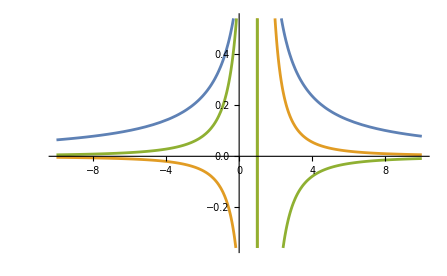

```mathematica
Plot[{ff/.{y->0,z->0,v->1/(√2),xp->1},
p/.{y->0,z->0,v->1/(√2),xp->1},
psix/.{y->0,z->0,v->1/(√2),xp->1}},{x,-10,10}]
```

```mathematica
dpdv = D[p,v]//FullSimplify
```

((x-xp) ((-1+2 v^2) x^2+2 (1-2 v^2) x xp+(-1+2 v^2) xp^2+(-1+v^4) (y^2+z^2)))/((-1+v^2) √(-(x-xp)^2/(-1+v^2)+y^2+z^2) ((x-xp)^2-(-1+v^2) (y^2+z^2))^2)

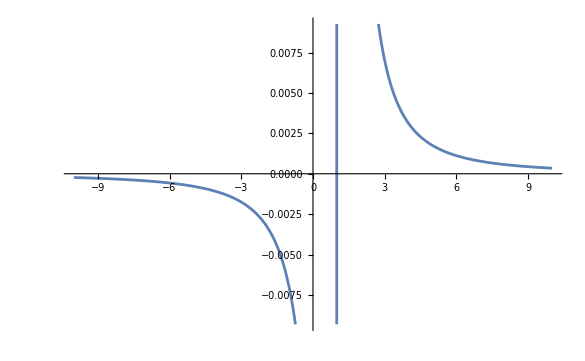

```mathematica
Plot[dpdv/.{y->0,z->0,v->0.7,xp->1},{x,-10,10}]
```

```mathematica
w[x_,y_,z_,v_]=((-1+2 v^2) x^3+(-1+v^4) x (y^2+z^2))/((-1+v^2) √(x^2/(1-v^2)+y^2+z^2) (x^2-(-1+v^2) (y^2+z^2))^2);
```

```mathematica
w[x,0,0,1/Sqrt[2]]//FullSimplify
```

0

```mathematica
1/Sqrt[2]
```

1/(√2)